```mathematica
Exit[]
```

```mathematica
PrependTo[$Path,"/home/data/promotion/Mathematica/Packages"];<<JoFin`
```

```mathematica
$Assumptions=Fold[And,True,{σ>0,a ∈ Reals,1>k1≥0,k0≥0,S0>0,K>0,r≥0,b ∈ Reals, rf≥0, γ>0}];
```

```mathematica
σ=.6;T=.1;r=0;μ=-.41;
γ=-.001Exp[- r];h=-2/3;
t = σ √T; mpr=(μ-r)/σ^2;
```

```mathematica
xx[W_,mpr_,t_]:=Exp[ t W+(mpr-1/2)t^2];
put[k_,t_]:=BlackScholesPut[4,k,1,0,t,.2]
```

```mathematica
NIntegrate[Max[0,1.1- 4xx[w,.2,.1]]Exp[-w^2/2],{w,-∞,∞}]/√(2π)-put[1.1,.1]
pr[a_]:=-Log[NIntegrate[Exp[-γ a( -xx[w,mpr,t])-w^2/2],{w,-∞,∞}]/√(2π)]/γ;
int[a_,w_]:=-γ a( -xx[w,mpr,t])-w^2/2;
pr2[a_,s_]:=-Log[NIntegrate[Exp[int[a,w]],{w,-∞,s}]/√(2π)]/γ;
s0=63;s0 xx[w,mpr,t]/.#&/@Solve[int[h s0,w]==0,w]
pr[h#]&/@{37.46351154411736,42.021013252888586,63.687969624999518,1000}
```

-8.8414×10^-30

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{56.3799,62.7408,2.33098×10^6}

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate :: errprec will be suppressed during this calculation.

{1000. Log[NIntegrate[Exp[-γ (-24.9757) (-xx[w,mpr,t])-w^2/2],{w,-∞,∞}]/(√(2 π))],1000. Log[NIntegrate[Exp[-γ (-28.014) (-xx[w,mpr,t])-w^2/2],{w,-∞,∞}]/(√(2 π))],1000. Log[NIntegrate[Exp[-γ (-42.4586) (-xx[w,mpr,t])-w^2/2],{w,-∞,∞}]/(√(2 π))],1000. Log[NIntegrate[Exp[1/3 (-γ) (-2000) (-xx[w,mpr,t])-w^2/2],{w,-∞,∞}]/(√(2 π))]}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{w→-(2 ProductLog[-(√(a ⅇ^(-t^2/2+mpr t^2) t^2 γ))/(√2)])/t},{w→-(2 ProductLog[(√(a ⅇ^(-t^2/2+mpr t^2) t^2 γ))/(√2)])/t}}

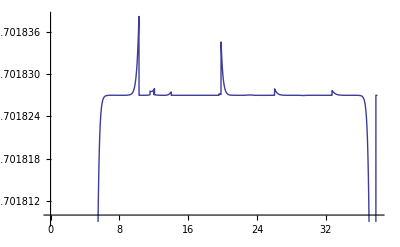

```mathematica
Plot[{pr2[h 62,s]},{s,0,38}]
```

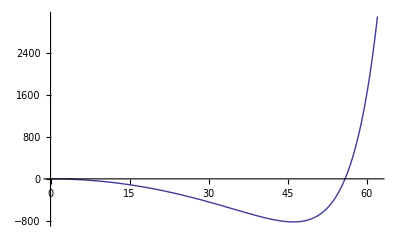

```mathematica
Plot[int[h 62,s],{s,0,62},PlotRange-> All]
```

## Demonstration für das Ausbleiben der Singularität

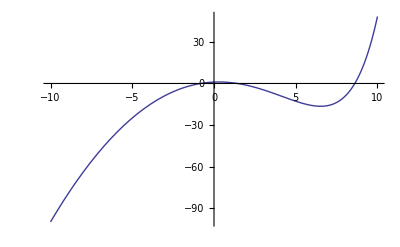

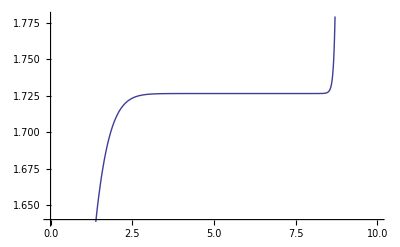

```mathematica
g[w_]:=Exp[.5w]-w^2
p[s_]:=Log[NIntegrate[Exp[g[w]],{w,-∞,s}]]
Plot[g[w],{w,-10,10}]
Plot[p[s],{s,0,10}]
```